# Type II model

## Modelling the Hamiltonian in Eq. (11) in Chiral anomaly and longitudinal magnetotransport in type-II Weyl semimetals

```mathematica
x[k_]:=k[[1]]
y[k_]:=k[[2]]
z[k_]:=k[[3]]
```

```mathematica
HI[k_]:=((Cos[y[k]] + Cos[z[k]] - 2) m  + 2 t (Cos[x[k]] - Cos[k0])) PauliMatrix[1] - 2 t Sin[y[k]] PauliMatrix[2] - 2 t Sin[z[k]] PauliMatrix[3]
```

```mathematica
HII[k_]:=HI[k] + γ (Cos[x[k]] - Cos[k0]) PauliMatrix[0]
```

```mathematica
Plot3D[HII[{kx, ky, 0}]/.{ γ->0, m->0.15, t->-0.005, k0->Pi/2}, {kx, -2, 2}, {ky, -2, 2}]
```

-Graphics3D-

```mathematica
HII[{kx, ky, 0}]/.{ γ->0, m->0.15, t->-0.005, k0->Pi/2}
```

{{0,-0.01 Cos[kx]+0.15 (-1+Cos[ky])-(0.+0.01 ⅈ) Sin[ky]},{-0.01 Cos[kx]+0.15 (-1+Cos[ky])+(0.+0.01 ⅈ) Sin[ky],0}}

### Plotting realistic briouille zone

```mathematica
eigvals=Eigenvalues[HII[{kx, ky, 0}]/.{ γ->0.15, m->0.15, t->-0.05, k0->Pi/2}]
```

{1/2 (0.3 Cos[kx]-√((0.175+0. ⅈ)+0.12 Cos[kx]+0.02 Cos[2 kx]-0.06 Cos[kx-ky]-0.18 Cos[ky]+0.025 Cos[2 ky]-0.06 Cos[kx+ky])),1/2 (0.3 Cos[kx]+√((0.175+0. ⅈ)+0.12 Cos[kx]+0.02 Cos[2 kx]-0.06 Cos[kx-ky]-0.18 Cos[ky]+0.025 Cos[2 ky]-0.06 Cos[kx+ky]))}

```mathematica
Plot3D[eigvals, {kx, -Pi, Pi}, {ky, -Pi, Pi}, ImageSize->Large]
```

-Graphics3D-

```mathematica
Plot3D[eigvals,{kx,-π,π},{ky,-π,π},PlotPoints->66,MaxRecursion->3,ImageSize->Large, ColorFunction->"Rainbow", PlotStyle->{Opacity[0.9], Specularity[Red, 200]}, Lighting->"ThreePoint"]
```

-Graphics3D-

```mathematica
Plot3D[eigvals,{kx,-π,π},{ky,-π,π},Filling->Bottom,PlotPoints->66,MaxRecursion->3,ImageSize->Large]
```

-Graphics3D-

### Ridgeline plot one dim

```mathematica
eigvals=Eigenvalues[HII[{kx, ky, 0}]/.{ m->0.15, t->-0.05, k0->Pi/2}]
```

{1/2 (2 γ Cos[kx]-√((0.175+0. ⅈ)+0.12 Cos[kx]+0.02 Cos[2 kx]-0.06 Cos[kx-ky]-0.18 Cos[ky]+0.025 Cos[2 ky]-0.06 Cos[kx+ky])),1/2 (2 γ Cos[kx]+√((0.175+0. ⅈ)+0.12 Cos[kx]+0.02 Cos[2 kx]-0.06 Cos[kx-ky]-0.18 Cos[ky]+0.025 Cos[2 ky]-0.06 Cos[kx+ky]))}

```mathematica
Table[
{kx, γ},
{γ, {0, 0.1, 0.15}},
{kx, -1, 1, 0.1}
]
```

{{{-1.,0},{-0.9,0},{-0.8,0},{-0.7,0},{-0.6,0},{-0.5,0},{-0.4,0},{-0.3,0},{-0.2,0},{-0.1,0},{0.,0},{0.1,0},{0.2,0},{0.3,0},{0.4,0},{0.5,0},{0.6,0},{0.7,0},{0.8,0},{0.9,0},{1.,0}},{{-1.,0.1},{-0.9,0.1},{-0.8,0.1},{-0.7,0.1},{-0.6,0.1},{-0.5,0.1},{-0.4,0.1},{-0.3,0.1},{-0.2,0.1},{-0.1,0.1},{0.,0.1},{0.1,0.1},{0.2,0.1},{0.3,0.1},{0.4,0.1},{0.5,0.1},{0.6,0.1},{0.7,0.1},{0.8,0.1},{0.9,0.1},{1.,0.1}},{{-1.,0.15},{-0.9,0.15},{-0.8,0.15},{-0.7,0.15},{-0.6,0.15},{-0.5,0.15},{-0.4,0.15},{-0.3,0.15},{-0.2,0.15},{-0.1,0.15},{0.,0.15},{0.1,0.15},{0.2,0.15},{0.3,0.15},{0.4,0.15},{0.5,0.15},{0.6,0.15},{0.7,0.15},{0.8,0.15},{0.9,0.15},{1.,0.15}}}

```mathematica
ListLinePlot3D[
{Table[
First[eigvals]/.{ky->0},
{γ, Subdivide[0.15, 3]},
{kx, -Pi, Pi, 0.1}
],
Table[
Last[eigvals]/.{ky->0},
{γ, Subdivide[0.15, 3]},
{kx, -Pi, Pi, 0.1}
]
},
Filling->Axis
]
```

-Graphics3D-

```mathematica
bottom=ListLinePlot3D[
Table[
First[eigvals]/.{ky->0},
{γ, Subdivide[0.15, 3]},
{kx, -Pi, Pi, 0.1}
]
,
Filling->Bottom
]
top=ListLinePlot3D[
Table[
Last[eigvals]/.{ky->0},
{γ, Subdivide[0.15, 3]},
{kx, -Pi, Pi, 0.1}
]
,
Filling->Top,
FillingStyle->{Opacity[0.1]}
]
Show[top,bottom, PlotRange->{-0.2, 0.2}, BoxRatios->{1, 2, 0.3}]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

```mathematica
Show[%143,ViewPoint->{0,∞,0}]
```

-Graphics3D-

```mathematica
r som bor sammen med noen som er smittet og trenger daglig testing for å slippe karantene kan få utdelt 5 test
```

```mathematica
Export["/home/thorvald/Documents/NTNU/10semester/notes/figures/typeIIridgeline.png",%143,"PNG"]
```

/home/thorvald/Documents/NTNU/10semester/notes/figures/typeIIridgeline.png

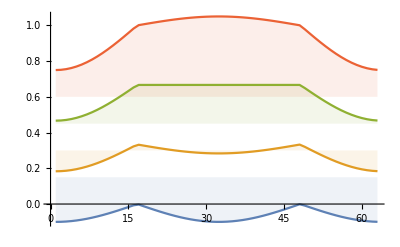

```mathematica
ListLinePlot[
Table[
γ /0.15+First[eigvals]/.{ky->0},
{γ, Subdivide[0.15, 3]},
{kx, -Pi, Pi, 0.1}
]
,
Filling->Table[n->n*0.15, {n, 4}],
FillingStyle->{Opacity[0.1]}
]
```

```mathematica
Table[n->n, {n, Subdivide[0.15, 3]}]
```

{0.→0.,0.05→0.05,0.1→0.1,0.15→0.15}

```mathematica
Table[n->n/0.15, {n, Subdivide[0.15, 3]}]
```

{0.→0.,0.05→0.333333,0.1→0.666667,0.15→1.}